```mathematica
fc[gnd_,d_,α_,len_]:=CDF[ParameterMixtureDistribution[PoissonDistribution[(gnd)*len*ρ],ρ\[Distributed]GammaDistribution[α,1/α]],d*len]
writeAlpha[α_]:= Export["alpha"<>ToString[α]<>"-c1-gl904-orf1.csv",N[Grid[Table[Join[{g+0.05},Table[fc[(g+0.05)/100,x,α,904.294],{x,{0,0.001,0.002, 0.003, 0.004, 0.005,0.01,0.015,0.02,0.025,0.03,.05}}]],{g,40,0,-.1}]],20],"TableHeadings"-> {"GND","100","99.9", "99.8", "99.7", "99.6", "99.5","99","98.5","98","97.5","97","95"}]
```

```mathematica
gl=904.294;
(*SetDirectory["/Users/smirarab/Research/projects/ongoing/ramunas/finalscripts"]*)
SetDirectory["/Users/home/Desktop/smirarab GORG-LGT master GNDModel"]
writeAlpha[3.31]
writeAlpha[5.28] 
writeAlpha[7.77]
```

/Users/home/Desktop/smirarab GORG-LGT master GNDModel

alpha3.31-c1-gl904-orf1.csv

alpha5.28-c1-gl904-orf1.csv

alpha7.77-c1-gl904-orf1.csv

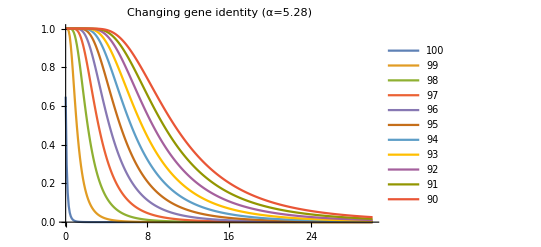

```mathematica
ListPlot[Table[{g,fc[(g+0.05)/100,1-x,5.28,gl]},{x,1,0.9,-0.01},{g,30,0,-.1}],PlotRange->All,Joined->True,PlotLegends->Range[100,90,-1],PlotLabel->"Changing gene identity (α=5.28)"]
```

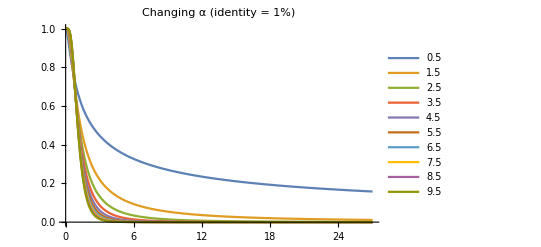

```mathematica
ListPlot[Table[{g,fc[(g+0.05)/100,1-0.99,α,gl]},{α,0.5,10,1},{g,27,0,-.1}],PlotRange->All,Joined->True,PlotLegends->Range[0.5,10,1],PlotLabel->"Changing α (identity = 1%)"]
```

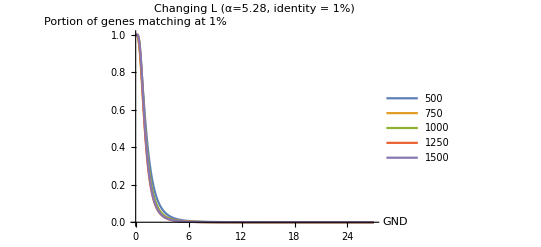

```mathematica
ListPlot[Table[{g,fc[(g+0.05)/100,1-0.99,5.28,gl]},{gl,500,1500,250},{g,27,0,-.1}],PlotRange->All,Joined->True,PlotLegends->Range[500,1500,250],PlotLabel->"Changing L (α=5.28, identity = 1%)",AxesLabel->{"GND","Portion of genes matching at 1%"}]
```

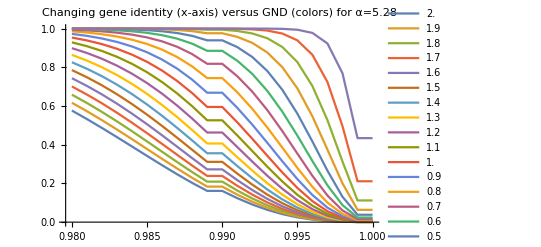

```mathematica
ListPlot[Table[{x,fc[(g)/100,1-x,5.28,gl]},{g,2,0.1,-.1},{x,1,0.98,-0.001}],PlotRange->All,Joined->True,PlotLegends->Range[2,0.1,-.1],PlotLabel->"Changing gene identity (x-axis) versus GND (colors) for α=5.28"]
```

```mathematica
{1,0.98,-0.05}
```

```mathematica
Range[1,0.98,-0.001]
```

{1.,0.9995,0.999,0.9985,0.998,0.9975,0.997,0.9965,0.996,0.9955,0.995,0.9945,0.994,0.9935,0.993,0.9925,0.992,0.9915,0.991,0.9905,0.99,0.9895,0.989,0.9885,0.988,0.9875,0.987,0.9865,0.986,0.9855,0.985,0.9845,0.984,0.9835,0.983,0.9825,0.982,0.9815,0.981,0.9805,0.98}

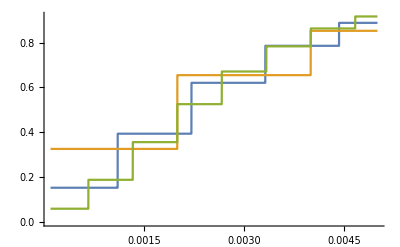

```mathematica
Plot[{fc[0.0025,d,5.28,904],fc[0.0025,d,5.28,500],fc[0.0025,d,5.28,1500]},{d,0.0001,0.005}]
```